Solve for the EPs

```mathematica
S=Solve[-x^3+d x+c==0,x]//FullSimplify
```

{{x→-(2 3^(1/3) d+2^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3))/(6^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))},{x→((-1)^(1/3) (2 3^(1/3) d-(-2)^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3)))/(6^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))},{x→(-2 (-3)^(2/3) d+(-6)^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3))/(3 2^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))}}

Plot the 3 branches to discover that it is the third (green) one we want

```mathematica
Plot3D[{x/.S[[1]],x/.S[[2]],x/.S[[3]]},{c,-4,4},{d,0,4}]
```

-Graphics3D-

Plot that branch with higher resolution

```mathematica
Plot3D[Evaluate[x/.S[[3]]],{c,-4,4},{d,0,4},MaxRecursion->7,WorkingPrecision->10,PlotStyle->Red,AxesLabel->{"\[beta_1","\[beta_2","y"}]
```

```mathematica
Plot3D[Evaluate[x/.S[[3]]],{c,0,4},{d,2,4},MaxRecursion->7,WorkingPrecision->10,PlotStyle->Red,AxesLabel->{"β_1","β_2","y"}]
```

```mathematica
p =-Graphics3D-
```

-Graphics3D-

```mathematica
p=-Graphics3D-
```

-Graphics3D-

```mathematica
Show[p,Boxed->False]
```

-Graphics3D-

Plot slices for different d values to see the cross-sectional shape of this branch

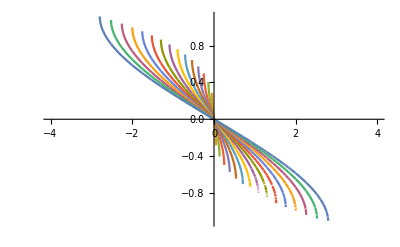

```mathematica
Plot[Evaluate[Table[Evaluate[x/.S[[3]]],{d,1/100000,4,1/4}]],{c,-4,4},PlotPoints->300]
```

Approximation for normal distribution CDF

Find the X such that normal CDF (mean=0,std=1) is 70%

```mathematica
x/.S[[3]]//FullSimplify
```

(-2 (-3)^(2/3) d+(-6)^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3))/(3 2^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))

The solution to the intersection

```mathematica
Solve[(x/.S[[3]])==-0.8]//FullSimplify
```

{{c→-0.512+0.8 d-(8.02489×10^-17+2.94609×10^-17 ⅈ) d^(3/2)},{c→-0.512+0.8 d+(8.02489×10^-17+2.94609×10^-17 ⅈ) d^(3/2)}}

```mathematica
Plot3D[-0.8,{c,-4,4},{d,0,4},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
p2=Plot3D[-0.8,{c,0,4},{d,2,4},PlotStyle->RGBColor[0.16,0.51,1.],AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Show[p,p2]
```

-Graphics3D-

```mathematica
Show[%106,Boxed->False]
```

-Graphics3D-

```mathematica
p
```

-Graphics3D-